## Asymmetric cylinder Scattering

This notebook is associated with the results presented in Chapter 3  of the Master Thesis  “Analogue Black hole binaries”.

### Clean Variables

In case you run into any of Mathematica problems, just clean all variables and go at it again

```mathematica
(*Clear all variables *)
ClearAll["Global`*"]
```

### Matrix entry functions

We begin by defining the helper functions for defining the entries of our matrix

```mathematica
(*Lambda_plus and Beta_plus*)
lambdaPlus[m_ ,Z_ , eps_,w_]:= (HankelH1[m,w] -ⅈ*Z*D[HankelH1[m,x],x]/.{x-> w} )+ eps*ⅈ*(Z/2) D[HankelH1[m,x],x]/.{x-> w} 

betaPlus[m_ ,Z_ , eps_,w_]:= eps*ⅈ*(Z/2) D[HankelH1[m,x],x]/.{x-> w} 

(*Lambda_minus and Beta_minus*)
lambdaMinus[m_ ,Z_ , eps_,w_]:= (HankelH2[m,w] -ⅈ*Z*D[HankelH2[m,x],x]/.{x-> w} )+ eps*ⅈ*(Z/2) D[HankelH2[m,x],x]/.{x-> w} 

betaMinus[m_ ,Z_ , eps_,w_]:= eps*ⅈ*(Z/2) D[HankelH2[m,x],x]/.{x-> w}
```

### Non Asymmetric functions

We can also use the exact result for the symmetric cylinder as a mean of comparison of both results

```mathematica
(*Lambda_plus and Beta_plus*)
Uniform…Cylinder…Absorbtion[m_ ,Z_ ,w_]:= (HankelH2[m,w] -ⅈ*Z*D[HankelH2[m,x],x]/.{x-> w} ) / (HankelH1[m,w] -ⅈ*Z*D[HankelH1[m,x],x]/.{x-> w} )
```

### Matrix equation components

Since the matrix is bi-diagonal, we can easily fill with with the desired entries

```mathematica
(*
	*Create matrix*
	matrixN must be odd!
*) 

lhsMatrix[matrixN_,Z_,eps_,w_] :=
(
(*Create main diagonal*)
mainDiagonal = Table[lambdaPlus[mm,Z,eps,w] ,{mm,-matrixN+1,matrixN-1,2}];

(*Create bidiagonal*)
diagUp =  Table[betaPlus[mm,Z,eps,w] ,{mm,-matrixN+3,matrixN-1,2}];
diagDn =  Table[betaPlus[mm,Z,eps,w] ,{mm,-matrixN+1,matrixN-3,2}];

(*Matrix*)
MM = DiagonalMatrix[diagDn,-1]+DiagonalMatrix[mainDiagonal] + DiagonalMatrix[diagUp,1];
Return[MM]
)

(*
	*Create RHS vector*
	matrixN must be odd!
*) 
rhsVector[matrixN_,Z_,eps_,w_] :=
(
(*Base vector entries*)
VV = {{-betaMinus[0,Z,eps,w]},{-lambdaMinus[0,Z,eps,w]},{-betaMinus[0,Z,eps,w]}};

(*Prepend zeros if matrix size is larger than 3*)
extraZeros = (matrixN-3)/2;

If[extraZeros == 0 , 
Null,
PrependTo[VV,Table[0,{i,1,extraZeros}]];
AppendTo[VV,Table[0,{i,1,extraZeros}]]
];

Return[Flatten[VV]]
)
```

### Solving the matrix equation

Choosing a set of parameters we can solve the cylinder matrix equation

```mathematica
(*Parameters to probe*)
omegaI = 0.0001;
omegaF = 5.0;
Nomega = 1200;
domega = (omegaF-omegaI)/(Nomega-1);
Omega…list = Table[omegaI + domega*(i-1) , {i,1,Nomega}];

mZ = 0.5;
mEps = 0.2;
mN = 7;

(*Create list of solutions*)
list…of…amps…0 = List[];
list…of…amps…2 = List[];
list…of…amps…4 = List[];

(*Probe frequency space*)
Do[
(*Get matrix*)
M = Inverse[lhsMatrix[mN,mZ,mEps,Omega…list[[i]]]//N];
v = rhsVector[mN,mZ,mEps,Omega…list[[i]]]//N;
sol = Dot[M,v];
AppendTo[list…of…amps…0 , sol[[(mN-1)/2+1]]];
AppendTo[list…of…amps…2 , sol[[(mN-1)/2+2]]];
AppendTo[list…of…amps…4 , sol[[(mN-1)/2+3]]];
,
{i,1,Nomega}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix … may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

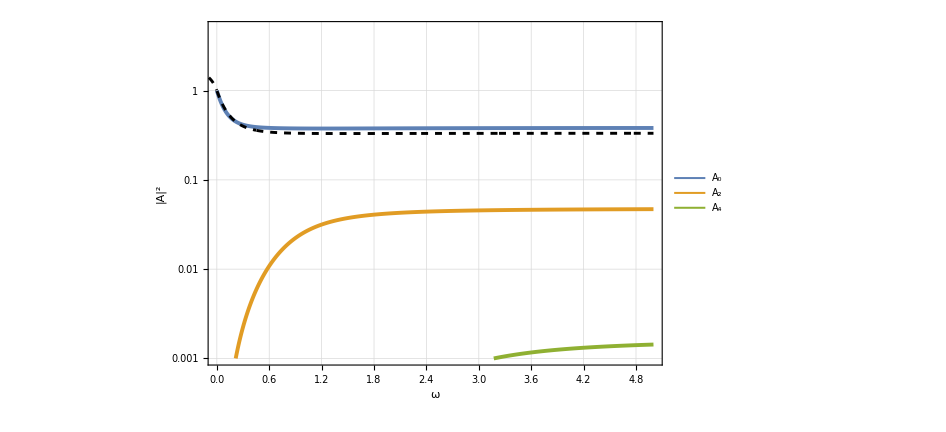

```mathematica
(*Plot results*)
p1 = ListLogPlot[
{	Table[{Omega…list[[i]],Abs[list…of…amps…0[[i]]]},{i,1,Nomega}],
	Table[{Omega…list[[i]],Abs[list…of…amps…2[[i]]]},{i,1,Nomega}],
	Table[{Omega…list[[i]],Abs[list…of…amps…4[[i]]]},{i,1,Nomega}]
},
PlotLegends-> {"A_0","A_2","A_4"},
FrameLabel->{"ω","|A|^2"},
PlotRange->{{omegaI,omegaF},{0.001,5}}, 
Joined->True,
PlotStyle->{Thickness[0.004]},
ImageSize->700,
PlotTheme->"Detailed"];

p2 = LogPlot[Abs[Uniform…Cylinder…Absorbtion[0 ,mZ ,w]],{w,-1,5},PlotStyle->{Dashed,Thickness[0.003],Black}];

Show[p1,p2]
```

And we can finally save the values to a text file

```mathematica
outdata = Table[{Omega…list[[i]],Abs[list…of…amps…0[[i]]] ,Abs[list…of…amps…2[[i]]] , Abs[list…of…amps…4[[i]]] },{i,1,Nomega}];

outname = "data/TM1_Matrix_Scattering_Amplitudes" <>
		"_reZ_"                 <>  ToString[NumberForm[Re[mZ],{5,2}]] <> 
		"_imZ_"                 <>  ToString[NumberForm[Im[mZ],{5,2}]] <> 
		"_eps_"          <>  ToString[NumberForm[mEps,{5,2}]] <>
		"_Nsize_"          <> ToString[NumberForm[mN,{5,2}]] <>
		".txt"

Export[
FileNameJoin[{NotebookDirectory[],outname}], outdata , "Table"];
```

data/TM1_Matrix_Scattering_Amplitudes_reZ_0.50_imZ_0_eps_0.20_Nsize_7.txt